```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/godfather/Documents/TaskDash/Flow

```mathematica
a = Import["out_data.txt","Table"][[4;;,2;;]]
```

{{0.,0.},{0.000287795,-0.83947},{0.000607589,-1.77165},{0.0009629,-2.8067},{0.00135771,-3.95589},{0.00179637,-5.23171},{0.00228378,-6.64796},{0.0028253,-8.21995},{0.00342702,-9.9646},{0.00409561,-11.9006},{0.00483848,-14.0487},{0.0056639,-16.4317},{0.00658101,-19.0747},{0.00760006,-22.0057},{0.00873228,-25.2553},{0.00999037,-28.8571},{0.0113882,-32.8483},{0.0129414,-37.2696},{0.0146671,-42.1656},{0.0165846,-47.5853},{0.0187152,-53.582},{0.0210824,-60.2138},{0.0237127,-67.5442},{0.0266352,-75.6417},{0.0298825,-84.5805},{0.0334906,-94.4403},{0.0374996,-105.306},{0.041954,-117.27},{0.0469034,-130.427},{0.0524027,-144.878},{0.058513,-160.728},{0.0653022,-178.083},{0.0728458,-197.051},{0.0812276,-217.737},{0.0905407,-240.24},{0.100889,-264.65},{0.112386,-291.039},{0.125161,-319.456},{0.139356,-349.912},{0.155128,-382.373},{0.172652,-416.737},{0.192123,-452.818},{0.213758,-490.311},{0.237797,-528.767},{0.264507,-567.539},{0.294184,-605.734},{0.327159,-642.144},{0.363798,-675.155},{0.404508,-702.644},{0.449741,-721.841},{0.5,-729.163},{0.550259,-721.74},{0.595492,-702.453},{0.636202,-674.883},{0.672841,-641.798},{0.705816,-605.323},{0.735493,-567.068},{0.762203,-528.242},{0.786242,-489.739},{0.807877,-452.202},{0.827348,-416.083},{0.844872,-381.683},{0.860644,-349.191},{0.874839,-318.706},{0.887614,-290.264},{0.899111,-263.852},{0.909459,-239.421},{0.918772,-216.899},{0.927154,-196.197},{0.934698,-177.213},{0.941487,-159.845},{0.947597,-143.983},{0.953097,-129.521},{0.958046,-116.354},{0.9625,-104.381},{0.966509,-93.5072},{0.970118,-83.6403},{0.973365,-74.695},{0.976287,-66.5917},{0.978918,-59.256},{0.981285,-52.6194},{0.983415,-46.6185},{0.985333,-41.195},{0.987059,-36.2955},{0.988612,-31.8711},{0.99001,-27.8771},{0.991268,-24.2727},{0.9924,-21.0209},{0.993419,-18.0879},{0.994336,-15.443},{0.995162,-13.0584},{0.995904,-10.9088},{0.996573,-8.97145},{0.997175,-7.2256},{0.997716,-5.65253},{0.998204,-4.2353},{0.998642,-2.95861},{0.999037,-1.80862},{0.999392,-0.772862},{0.999712,0.159955},{1.,1.}}

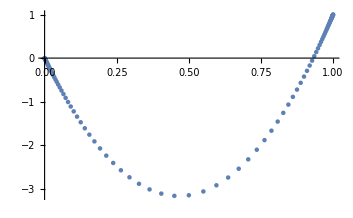

```mathematica
ListPlot[a]
```

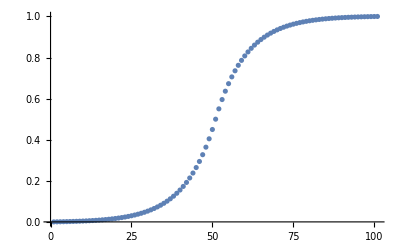

```mathematica
ListPlot[a[[;;,1]]]
```

```mathematica
A = Import["turb_out.txt","Table"]
```

{{0.,0.},{0.001,-0.000309359},{0.00202299,-0.00062312},{0.00314829,-0.000965089},{0.00438611,-0.00133742},{0.00574772,-0.00174235},{0.00724548,-0.00218216},{0.00889303,-0.00265916},{0.0107053,-0.00317564},{0.0126989,-0.00373384},{0.0148917,-0.00433582},{0.0173039,-0.00498344},{0.0199573,-0.00567821},{0.022876,-0.00642115},{0.0260866,-0.0072126},{0.0296183,-0.00805199},{0.0335031,-0.00893757},{0.0377764,-0.00986603},{0.042477,-0.0108321},{0.0476477,-0.0118278},{0.0533355,-0.0128422},{0.059592,-0.0138601},{0.0664742,-0.0148613},{0.0740446,-0.0158193},{0.0823721,-0.0166996},{0.0915323,-0.017458},{0.101609,-0.0180383},{0.112692,-0.0183692},{0.124885,-0.0183614},{0.138296,-0.0179029},{0.153049,-0.0168541},{0.169277,-0.0150417},{0.187127,-0.0122508},{0.206763,-0.00821642},{0.228362,-0.00261151},{0.252121,0.00496603},{0.278257,0.01501},{0.307005,0.0281259},{0.338629,0.0450551},{0.373415,0.0667042},{0.411679,0.0941809},{0.45377,0.128837},{0.5,0.172322},{0.54623,0.221424},{0.588321,0.270938},{0.626585,0.319979},{0.661371,0.367892},{0.692995,0.414201},{0.721743,0.458575},{0.747879,0.500794},{0.771638,0.540728},{0.793237,0.578316},{0.812873,0.613547},{0.830723,0.646453},{0.846951,0.677091},{0.861704,0.705544},{0.875115,0.731904},{0.887308,0.756278},{0.898391,0.778773},{0.908468,0.799503},{0.917628,0.818579},{0.925955,0.836112},{0.933526,0.852209},{0.940408,0.866973},{0.946665,0.880502},{0.952352,0.89289},{0.957523,0.904226},{0.962224,0.914592},{0.966497,0.924066},{0.970382,0.93272},{0.973913,0.940621},{0.977124,0.947833},{0.980043,0.954413},{0.982696,0.960414},{0.985108,0.965885},{0.987301,0.970872},{0.989295,0.975417},{0.991107,0.979557},{0.992755,0.983329},{0.994252,0.986764},{0.995614,0.989892},{0.996852,0.992739},{0.997977,0.995331},{0.999,0.997691},{1.,1.}}

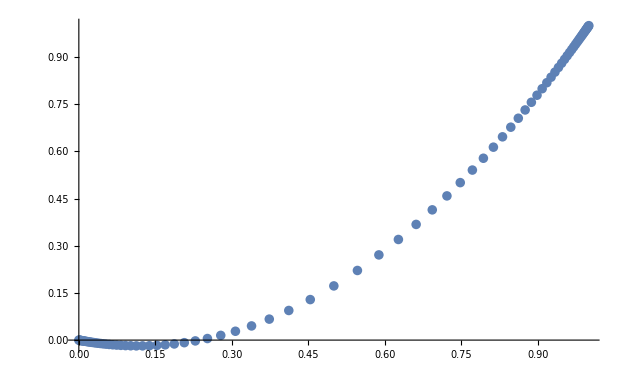

```mathematica
ListPlot[{A}]
```

```mathematica
a = Import["turb_out_plus.txt","Table"]
```

{{-Infinity,0.},{-8.9203,-0.000174301},{-8.22033,-0.000352705},{-7.78317,-0.000549074},{-7.45728,-0.000765253},{-7.19326,-0.00100329},{-6.96875,-0.00126545},{-6.77175,-0.00155429},{-6.59511,-0.00187263},{-6.43423,-0.00222368},{-6.28605,-0.00261104},{-6.14844,-0.00303884},{-6.01992,-0.00351181},{-5.89945,-0.00403548},{-5.78637,-0.00461635},{-5.68027,-0.0052623},{-5.58104,-0.00598303},{-5.48881,-0.00679089},{-5.40404,-0.00770214},{-5.32755,-0.0087392},{-5.2607,-0.00993463},{-5.20571,-0.0113388},{-5.16615,-0.0130359},{-5.14823,-0.0151821},{-5.16382,-0.0181094},{-5.2399,-0.0227001},{-5.46384,-0.0325719},{-7.28272,-0.226795},{-5.18991,-0.0309861},{-4.72185,-0.0209513},{-4.39463,-0.0157363},{-4.12569,-0.0118702},{-3.88882,-0.00843333},{-3.6723,-0.0050329},{-3.46983,-0.00144293},{-3.27761,0.00249959},{-3.09321,0.00693411},{-2.91493,0.0119948},{-2.74159,0.0178207},{-2.57227,0.0245623},{-2.4063,0.0323867},{-2.24315,0.0414825},{-2.08538,0.0522131},{-1.94512,0.0637026},{-1.82802,0.0746769},{-1.729,0.0850742},{-1.64433,0.0948622},{-1.57132,0.10403},{-1.5079,0.112582},{-1.45249,0.120532},{-1.40384,0.127902},{-1.36095,0.134717},{-1.32299,0.141007},{-1.2893,0.146802},{-1.25932,0.152133},{-1.23257,0.157031},{-1.20867,0.161525},{-1.18726,0.165645},{-1.16806,0.169419},{-1.15082,0.172873},{-1.13532,0.176032},{-1.12136,0.178919},{-1.10878,0.181557},{-1.09744,0.183965},{-1.0872,0.186164},{-1.07796,0.188169},{-1.0696,0.189999},{-1.06205,0.191666},{-1.05521,0.193187},{-1.04902,0.194572},{-1.04342,0.195834},{-1.03834,0.196984},{-1.03374,0.19803},{-1.02957,0.198984},{-1.02579,0.199852},{-1.02237,0.200642},{-1.01926,0.201361},{-1.01643,0.202015},{-1.01387,0.202611},{-1.01155,0.203153},{-1.00944,0.203646},{-1.00753,0.204094},{-1.00579,0.204502},{-1.00419,0.204869},{-1.00319,0.205343}}

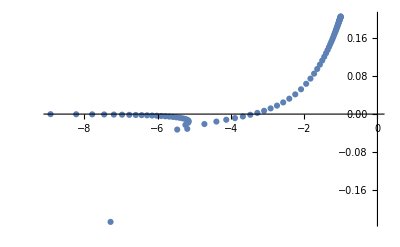

```mathematica
ListPlot[a]
```

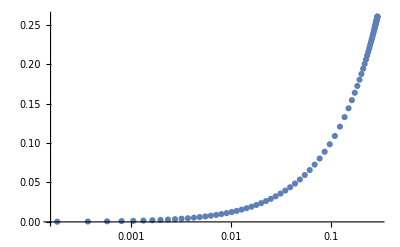

```mathematica
ListPlot[a, ScalingFunctions->{"Log",None}]
```